```mathematica
(*
 rectset
analytical expressions for rectangle electrode in a SET
Carmelo Mordini, 04/2023
ref: Analytic model for electrostatic fields in surface-electrode ion traps
M.G.House
Phys.Rev.A 78,033402
https://journals.aps.org/pra/abstract/10.1103/PhysRevA.78.033402
*)
```

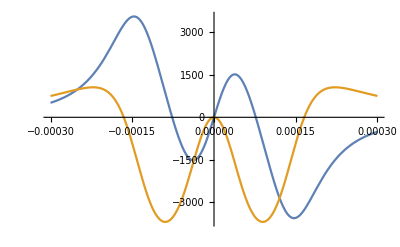

```mathematica
(*Infinite along x RF electrodes for five-wire trap*)
(* symmetrically positioned around y = 0, separated by a, of width w *)

ϕ0[x_,y_,z_,y1_,y2_]:=1/π(ArcTan[(y2-y)/z]- ArcTan[(y1 - y)/z]); (*23*)
E0[x_,y_,z_,y1_,y2_]=D[ϕ0[x,y,z,y1,y2],{{x,y,z}}];

ϕRF[x_,y_,z_,a_,w_] = ϕ0[x,y,z,-a/2-w,-a/2]+ϕ0[x,y,z,a/2,a/2+w];
ERF[x_,y_,z_,a_,w_]=D[ϕRF[x,y,z,a,w],{{x,y,z}}];
d1ERF[x_,y_,z_,a_,w_]=D[ERF[x,y,z,a,w],{{x,y,z}}];
d2ERF[x_,y_,z_,a_,w_]=D[d1ERF[x,y,z,a,w],{{x,y,z}}];

um = 10^-6;
rfgeom ={a->70 um, w->105um};
toplot =ERF[0,y,70um,a,w][[2;;3]]/.rfgeom;
Plot[toplot, {y, -300um, 300um}]
```

```mathematica
ϕps[x_,y_,z_,a_,w_]=ERF[x,y,z,a,w].ERF[x,y,z,a,w]//FullSimplify;
Eps[x_,y_,z_,a_,w_]=2 d1ERF[x,y,z,a,w] . ERF[x,y,z,a,w];
Hps[x_,y_,z_,a_,w_]=2 (d1ERF[x,y,z,a,w] . d1ERF[x,y,z,a,w] + d2ERF[x,y,z,a,w] . ERF[x,y,z,a,w]);
```

1/2 √(a (a+2 w))

1/2 √(a^2+2 a w+2 (a+w) √(a (a+2 w)))

(4 w^2)/(π^2 (a+w)^2 (a+w+√(a (a+2 w)))^2)

{70.,130.958}

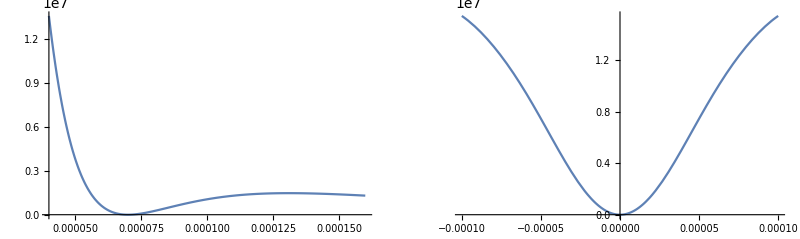

```mathematica
efieldNulls=Solve[Assuming[{a>0,w>0},FullSimplify@Reduce[{Eps[0,0,z,a,w]==0,z>0},z,Reals]],z];
znull = efieldNulls[[1,1,2]]
zsaddle = efieldNulls[[2,1,2]]
trapdepth=ϕps[0,0,zsaddle,a,w]//FullSimplify
{znull/um,zsaddle/um}/.rfgeom//N

pϕpsz=Plot[ϕps[0,0,z,a,w]/.rfgeom, {z, 40um, 160um},PlotRange->Full];
pϕpsy=Plot[ϕps[0,y,znull,a,w]/.rfgeom, {y, -100um, 100um},PlotRange->Full];
GraphicsGrid[{{pϕpsz,pϕpsy}}]
```

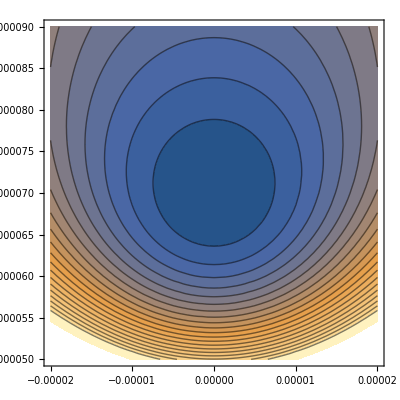

```mathematica
ContourPlot[ϕps[0,y,z,a,w]/.rfgeom,{y, -20um, 20um}, {z, 50um, 90um},Contours->20]
```

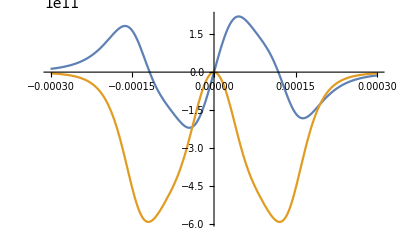

```mathematica
toplot =Eps[0,y,70um,a,w][[2;;3]]/.rfgeom;
Plot[toplot, {y, -300um, 300um}]
```

```mathematica
(*Finite electrode*)
ϕ1[x_,y_,z_,x1_,x2_,y1_,y2_]=1/(2π)(ArcTan[(x2-x)(y2-y)/(z Sqrt[z^2+(x2-x)^2+(y2-y)^2])]-ArcTan[(x1-x)(y2-y)/(z Sqrt[z^2+(x1-x)^2+(y2-y)^2])]-ArcTan[(x2-x)(y1-y)/(z Sqrt[z^2+(x2-x)^2+(y1-y)^2])]+ArcTan[(x1-x)(y1-y)/(z Sqrt[z^2+(x1-x)^2+(y1-y)^2])]); (*22*)
E1[x_,y_,z_,x1_,x2_,y1_,y2_]=D[ϕ1[x,y,z,x1,x2,y1,y2],{{x,y,z}}];
H1[x_,y_,z_,x1_,x2_,y1_,y2_]=D[E1[x,y,z,x1,x2,y1,y2],{{x,y,z}}];
```

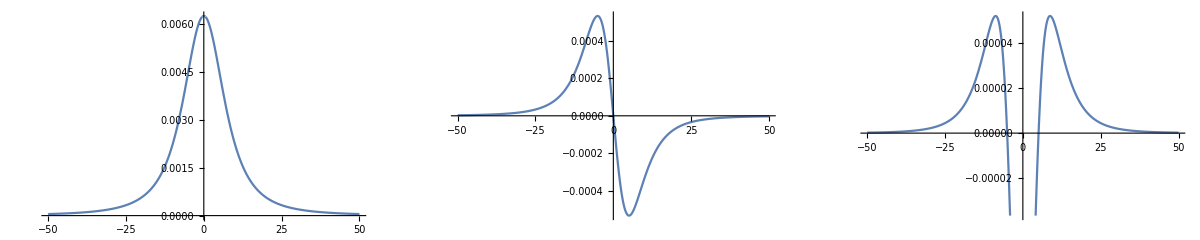

```mathematica
pϕ1=Plot[ϕ1[x,0,10,-0.5,0.5,-2,2], {x, -50, 50}];
pE1=Plot[E1[x,0,10,-0.5,0.5,-2,2][[1]], {x, -50, 50}];
pH1=Plot[H1[x,0,10,-0.5,0.5,-2,2][[1,1]], {x, -50, 50}];
GraphicsGrid[{{pϕ1,pE1,pH1}}]
```

```mathematica
(*Export to Python*)
```

```mathematica
ToPython[expr_]:=Module[{expr1,expr2},
expr1=Refine[expr,{x∈Reals,y∈Reals,z>0},TimeConstraint->1];
expr2=expr1/.a_Real:>ToString@ScientificForm[a,NumberFormat->(If[#3≠"",Row[{#1,"e",#3}],ToString[#1]]&)];
StringDelete[ToString[FortranForm[expr2]],"\""]]
```

```mathematica
dir = FileNameJoin[{NotebookDirectory[],"rectset"}];
CreateDirectory[dir]
```

D:\Scratch\pytrans-examples\deps\rectset\src\rectset

```mathematica
fileHeader = StringRiffle[{
"#!/usr/bin/env python",
"# -*- coding:utf-8 -*-",
"#",
"# Created: "<> DateString[Today],
"# Author: Carmelo Mordini <cmordini@phys.ethz.ch>",
"#",
"# Analytical functions for rectangle electrodes in a SET - generated in Mathematica",
"# ref: M.G.House, Phys.Rev.A 78, 033402 (2008)",
"# https://doi.org/10.1103/PhysRevA.78.033402",
"#",
"# flake8: noqa",
""}, "\n"]<>"\n";
file=FileNameJoin[{dir, "__init__.py"}];
Put[file];
```

```mathematica
file=FileNameJoin[{dir, "pseudopotential.py"}];

yelpot = ToPython[ϕ0[x,y,z,y1,y2]];
yelgrad = Map[ToPython,E0[x,y,z,y1,y2]];

rfpot = ToPython[ϕRF[x,y,z,a,w]];
rfgrad = Map[ToPython,ERF[x,y,z,a,w]];

znullPy = ToPython[znull];
zsaddlePy = ToPython[zsaddle];
trapdepthPy = ToPython[trapdepth];

pspot = ToPython[ϕps[x,y,z,a,w]];
psgrad = Map[ToPython,Eps[x,y,z,a,w]];
pshess = Map[ToPython,Hps[x,y,z,a,w],{2}];

zeros = "np.zeros_like(x)";
yelgrad[[1]] = zeros;
rfgrad[[1]] = zeros;
psgrad[[1]] = zeros;

pshess[[1]] = {zeros, zeros, zeros};

fileBody = StringRiffle[{
"import numpy as np",
"from numpy import abs as Abs",
"from numpy import sqrt as Sqrt",
"from numpy import arctan as ArcTan",
"from numpy import pi as Pi",
"",
"",
"elementary_charge = 1.602176634e-19",
"atomic_mass = 1.6605390666e-27",
"K = elementary_charge / (4 * atomic_mass * (2*Pi*1e6)**2)",
"",
"def infx_el_potential(x, y, z, y1, y2):",
"    \"\"\"potential of one electrode extending between y1 and y2, infinite along x\"\"\"",
"    x, y, z = np.broadcast_arrays(x, y, z)",
"    return "<> yelpot,
"",
"def infx_el_gradient(x, y, z, y1, y2):",
"    x, y, z = np.broadcast_arrays(x, y, z)",
"    return np.stack(["<>StringRiffle[yelgrad,","]<>"], axis=-1)",
"",
"def infx_rf_pair_potential(x, y, z, a, w):",
"    \"\"\"potential of a pair of symmetric electrodes",
"        separated by a, of width w, infinite along x",
"    \"\"\"",
"    x, y, z = np.broadcast_arrays(x, y, z)",
"    return "<> rfpot,
"",
"def infx_rf_pair_gradient(x, y, z, a, w):",
"    x, y, z = np.broadcast_arrays(x, y, z)",
"    return np.stack(["<>StringRiffle[rfgrad,","]<>"], axis=-1)",
"",
"def rf_null_z(a, w):",
"    r\"\"\"position of RF null for symmetric infinite electrode pair",
"            $$ z_0 = \\frac{1}{2} \\sqrt{a^2 (a + 2w)} $$",
"    \"\"\"",
"    return "<> znullPy,
"",
"def rf_saddle_z(a, w):",
"    r\"\"\"position of RF saddle point for symmetric infinite electrode pair",
"            $$ z_S = \\frac{1}{2} \\sqrt{a^2 + 2aw + 2(a+w)\\sqrt{a(a+2w)}} $$",
"    \"\"\"",
"    return "<> zsaddlePy,
"",
"def rf_trap_depth(a, w):",
"    r\"\"\"pseudopotential at the rf saddle point",
"            $$ \\phi_D = \\left[\\frac{2w}{\\pi (a+w) (a + w + \\sqrt{a(a+2w)})}\\right]^2 $$",
"    \"\"\"",
"    return "<> trapdepthPy,
"",
"def pseudo_potential(x, y, z, a, w):",
"    x, y, z = np.broadcast_arrays(x, y, z)",
"    return K * "<> pspot,
"",
"def pseudo_gradient(x, y, z, a, w):",
"    x, y, z = np.broadcast_arrays(x, y, z)",
"    return K * np.stack(["<>StringRiffle[psgrad,","]<>"], axis=-1)",
"",
"def pseudo_hessian(x, y, z, a, w):",
"    x, y, z = np.broadcast_arrays(x, y, z)",
"    xx = "<>pshess⟦1,1⟧,
"    xy = "<>pshess⟦1,2⟧,
"    xz = "<>pshess⟦1,3⟧,
"    yy = "<>pshess[[2,2]],
"    yz = "<>pshess⟦2,3⟧,
"    zz = "<>pshess⟦3,3⟧,
"    h1 = np.asarray([[xx,xy,xz],[xy,yy,yz],[xz,yz,zz]])",
"    return K * h1.transpose(tuple(_ for _ in range(2, h1.ndim)) + (0, 1))"
}, "\n"]<>"\n";
fileBody = StringReplace[fileBody,"a/2."->"0.5*a"];
Put[file];

WriteString[file, fileHeader];
WriteString[file, fileBody];

Close[file];
```

```mathematica
file=FileNameJoin[{dir, "rectangle_electrode.py"}];

pot1 = ToPython[ϕ1[x,y,z,x1,x2,y1,y2]];
grad1 = Map[ToPython,E1[x,y,z,x1,x2,y1,y2]];
hess1 = Map[ToPython,H1[x,y,z,x1,x2,y1,y2],{2}];

fileBody = StringRiffle[{
"import numpy as np",
"from numpy import arctan as ArcTan",
"from numpy import sqrt as Sqrt",
"from numpy import pi as Pi",
"",
"",
"def rect_el_potential(x, y, z, x1, x2, y1, y2):",
"    return "<> pot1,
"",
"def rect_el_gradient(x, y, z, x1, x2, y1, y2):",
"    return np.stack(["<>StringRiffle[grad1,","]<>"], axis=-1)",
"",
"def rect_el_hessian(x, y, z, x1, x2, y1, y2):",
"    xx = "<>hess1⟦1,1⟧,
"    xy = "<>hess1⟦1,2⟧,
"    xz = "<>hess1⟦1,3⟧,
"    yy = "<>hess1[[2,2]],
"    yz = "<>hess1⟦2,3⟧,
"    h1 = np.asarray([[xx,xy,xz],[xy,yy,yz],[xz,yz,-xx-yy]])",
"    return h1.transpose(tuple(_ for _ in range(2, h1.ndim)) + (0, 1))"
}, "\n"]<>"\n";

Put[file];

WriteString[file, fileHeader];
WriteString[file, fileBody];

Close[file];
```

```mathematica
ϕps[x,y,z,a,w]
```

(64 w^2 ((a^2+2 a w+4 y^2)^2-8 (a^2+2 a w-4 y^2) z^2+16 z^4))/(π^2 ((a-2 y)^2+4 z^2) ((a+2 w-2 y)^2+4 z^2) ((a+2 y)^2+4 z^2) ((a+2 (w+y))^2+4 z^2))

```mathematica
pspot
```

(64*w**2*((a**2 + 2*a*w + 4*y**2)**2 - 8*(a**2 + 2*a*w - 4*y**2)*z**2 + 16*z**4))/(Pi**2*((a - 2*y)**2 + 4*z**2)*((a + 2*w - 2*y)**2 + 4*z**2)*((a + 2*y)**2 + 4*z**2)*((a + 2*(w + y))**2 + 4*z**2))

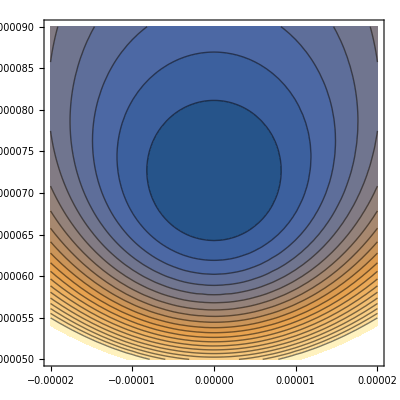

```mathematica
ContourPlot[ϕps[0,y,z,70um,110um],{y, -20um, 20um}, {z, 50um, 90um},Contours->20]
```

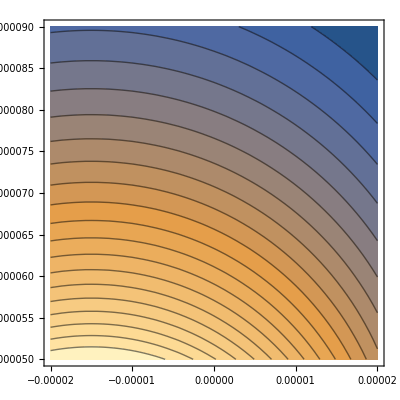

```mathematica
ContourPlot[ϕ1[0,y,z,-3000um,3000um,-30um,0],{y, -20um, 20um}, {z, 50um, 90um},Contours->20]
```

```mathematica
pot1
```

(ArcTan(((-x + x1)*(-y + y1))/(z*Sqrt((-x + x1)**2 + (-y + y1)**2 + z**2))) - ArcTan(((-x + x2)*(-y + y1))/(z*Sqrt((-x + x2)**2 + (-y + y1)**2 + z**2))) - ArcTan(((-x + x1)*(-y + y2))/(z*Sqrt((-x + x1)**2 + (-y + y2)**2 + z**2))) + ArcTan(((-x + x2)*(-y + y2))/(z*Sqrt((-x + x2)**2 + (-y + y2)**2 + z**2))))/(2.*Pi)

```mathematica
f[x_,y_]:=ArcTan[y/x]
f2[x_,y_]:=ArcTan[x,y]
```

```mathematica
f[x,y]
f2[x,y]
```

ArcTan[y/x]

ArcTan[x,y]

```mathematica
D[f[x,y], {{x,y}}]
D[f2[x,y], {{x,y}}]
```

{-y/(x^2 (1+y^2/x^2)),1/(x (1+y^2/x^2))}

{-y/(x^2+y^2),x/(x^2+y^2)}

```mathematica
ToPython[f[x,y]]
```

ArcTan(y/x)

```mathematica
ToPython[f2[x,y]]
```

ArcTan(x,y)